```mathematica
Clear[x]; (* IMPORTANT! Otherwise, wrong result when evaluating total notebook *)
(* What formats can we import? Use "Elements" *)
Import["c:/coding/c_kode/polyphoney.txt", "Elements"]
```

{Data,Lines,Plaintext,String,Words}

```mathematica
myLines=Import["c:/coding/c_kode/polyphoney.txt", "Data"]
```

{{1,4},{1,5},{1,6},{0,6},{0,5},{1,12},{1,15},{1,20},{1,21},{1,22},{1,23},{0,21},{0,22},{0,23},{1,25},{1,26},{1,28},{1,32},{1,33},{0,25},{0,28},{0,33},{0,32}}

```mathematica
Length[myLines]
```

23

```mathematica
myLines[[1]]
```

{1,4}

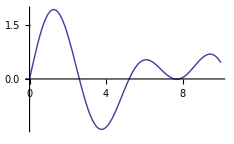

-Graphics-

```mathematica
(* Export plot to file *)
Plot[Sin[x]+Sin[x Sqrt[2]],{x,0,10}]
Export["C:\\coding\\Mathematics\\sinplot.jpg",%,"JPG"];
Plot[Sin[x]+Sin[x Sqrt[2]],{x,0,10}]
Export["C:\\coding\\Mathematics\\sinplot.gif",%,"GIF"];
```

```mathematica
myPolyStatus = {0, 0, 0, 0};
myPolyCounters = {0, 0, 0, 0};
myStatus = Array[s,{Length[myLines], 4}]; (* Each array element has 4 child-elements *) 
i = 1;

While [i <= Length[myLines],
If[myLines[[i, 1]] == 1,
{myStatus[[i, 1]] = "ON"; myStatus[[i, 2]] =  1} ,
{myStatus[[i, 1]] = "OFF"; myStatus[[i, 2]] = - 1}];
i++;
]
myStatus
```

{{ON,1,s[1,3],s[1,4]},{ON,1,s[2,3],s[2,4]},{ON,1,s[3,3],s[3,4]},{OFF,-1,s[4,3],s[4,4]},{OFF,-1,s[5,3],s[5,4]},{ON,1,s[6,3],s[6,4]},{ON,1,s[7,3],s[7,4]},{ON,1,s[8,3],s[8,4]},{ON,1,s[9,3],s[9,4]},{ON,1,s[10,3],s[10,4]},{ON,1,s[11,3],s[11,4]},{OFF,-1,s[12,3],s[12,4]},{OFF,-1,s[13,3],s[13,4]},{OFF,-1,s[14,3],s[14,4]},{ON,1,s[15,3],s[15,4]},{ON,1,s[16,3],s[16,4]},{ON,1,s[17,3],s[17,4]},{ON,1,s[18,3],s[18,4]},{ON,1,s[19,3],s[19,4]},{OFF,-1,s[20,3],s[20,4]},{OFF,-1,s[21,3],s[21,4]},{OFF,-1,s[22,3],s[22,4]},{OFF,-1,s[23,3],s[23,4]}}

```mathematica
(* Manipulate[BarChart[myLines[[x]]],
{x, 1,Length[myLines], 1}] *)(* Note: Step size as last number *)
```

```mathematica
a = {{1,2,3,4},{2,4,5,6},{-2,5,8,10}};
```

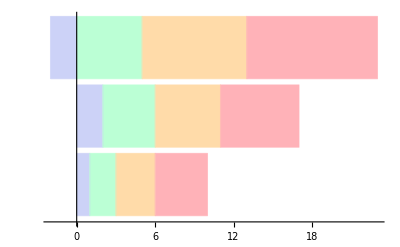

```mathematica
BarChart[a,ChartLayout->"Stacked",BarOrigin->Left]
```

```mathematica
(* Some random stuff... *)
RandomInteger[{1, 16}, 16]
```

{10,13,11,15,6,15,3,6,15,4,11,10,2,16,8,9}

```mathematica
(* NOTE: Remember semicolon after everything but last statement! *)
myFifteenModule[maxnum_]:=
Module[{},
x = 0;
i = 0;
randomInt = 0;
fifteenArray = ConstantArray[0, maxnum];

While [x<maxnum,
	{
randomInt=RandomInteger[{1, maxnum}];
	
For [i=0, i <x, i++,
		If [randomInt==fifteenArray[[i + 1]],
	Break[]
]; (* End If *)
];(* End For *)
	
	If [i≥x,
{fifteenArray[[x + 1]]=randomInt; x++}
] (* End If, note: semicolon not needed *)
}
]; (* End While *)

fifteenArray
]
```

{14,9,11,12,4,10,8,13,15,7,16,5,6,2,1,3}

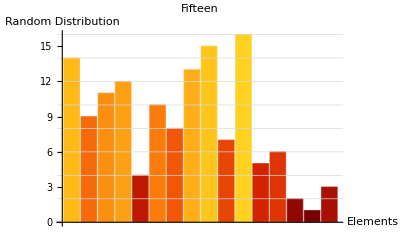

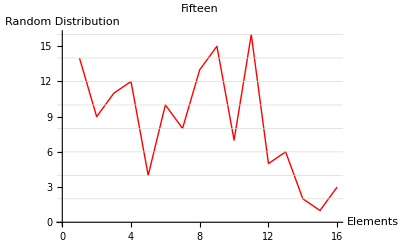

```mathematica
a = myFifteenModule[16]; (* Tip: Overlay two plots with Show[Plot1, Plot2] *)
a
BarChart[a, AxesLabel->{"Elements", "Random Distribution"},
GridLines->{Range[0], Range[0, Max[a], 2]},
PlotLabel->"Fifteen", GridLinesStyle->LightGray,
ChartStyle->{Red,Green,Blue},ColorFunction->ColorData["SolarColors"]]
ListLinePlot[a,
AxesLabel->{"Elements", "Random Distribution"},
GridLines->{Range[0], Range[0, Max[a], 2]},
PlotLabel->"Fifteen",PlotStyle->Red,
GridLinesStyle->LightGray]
```

```mathematica
(* Some Limits examples *)
Limit[(2 n^2  + 5)/(3 n^2 + 1), {n->100}](* Not so close here... *)
```

{20005/30001}

```mathematica
N[%]
```

{0.666811}

```mathematica
Limit[(2 n^2  + 5)/(3 n^2 + 1), {n->1000000}] 
(* Getting very close here... *)
```

{2000000000005/3000000000001}

```mathematica
N[%]
```

{0.666667}

```mathematica
Limit[(2 n^2  + 5)/(3 n^2 + 1), {n->∞}]
```

{2/3}

```mathematica
N[%]
```

{0.666667}

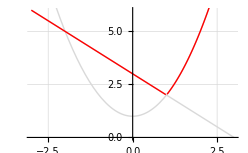

```mathematica
Show[Plot[3 - x, {x, -3, 3}, PlotStyle->LightGray,
GridLines->Automatic, GridLinesStyle->LightGray],
Plot[x^2 + 1, {x, -3, 3}, PlotStyle->LightGray],
Plot[3 - x, {x, -3, 0.98}, PlotStyle->Red],
Plot[x^2 + 1, {x, 1.02, 3}, PlotStyle->Red]]
(* Limit=2. See below for better way with PlotRange *)
```

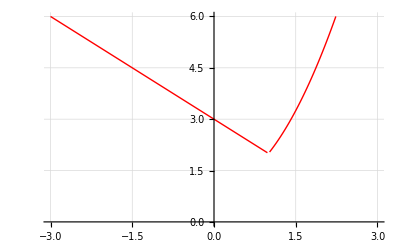

```mathematica
Show[Plot[3 - x, {x, -3, 0.98}, PlotStyle->Red,
GridLines->Automatic, GridLinesStyle->LightGray,
PlotRange->{{-3, 3},{0, 6}},
PlotRangeClipping -> False],
Plot[x^2 + 1, {x, 1.02, 3}, PlotStyle->Red,
PlotRange->{{-3, 3}, {0, 6}},
PlotRangeClipping -> False]
]
```

```mathematica
(* The fraction 3/4: 3=Numerator. 4=Denominator *)

(* Add fractions: Make the denominators equal.
Do: (2*2)/(1*2) = 4/2.
Then: (1/2)+(4/2) = 5/2. Or simplified: (1+4)/2 = 5/2.
NOTE: Can also do: (a/b)+(c/d) = ((a*d)+(b*c))/(b*d) *)
1/2 +2/1
```

5/2

```mathematica
(* Divide fractions: Switching elements in fraction no. 2 and multiplying, you get: (1/2)*(1/3) = (1*1)/(2*3) = 1/6 *)
1/2 / (3/1)
```

1/6

```mathematica
(* Multiply fractions: Multiply numerator with numerator, and denominator with denominator: (2*1)/(3*5) *)
2/3 * 1/5
```

2/15

```mathematica
(* Some other fraction examples *)
3/2-1 (* This equals: 3/2 - 2/2 = 1/2 *)
```

1/2

```mathematica
-5/2-1 (* This equals: -5/2 - 2/2 = -7/2 *)
```

-7/2

```mathematica
(* Additive inverse result is zero: -3 + 3 = 0.  Multiplicative inverse result is one: -3 * -1/3 = 1 *)
-3 * -1/3
```

1

```mathematica
1/x^4*x^7*3/x (* This is: x^-4*x^7*3 x^-1 = 3 x^(-4+7-1) = 3 x^2*)
```

768

```mathematica
myVar = 20;
{myVar^2-myVar-42, (myVar-7)(myVar+6)}
```

{338,338}

```mathematica
{myVar^2-9, (myVar+3)(myVar-3)} 
(* Factoring here: Difference ok, sum not ok: {myVar^2+ 9, (myVar+3)(myVar+3)} WRONG! See: Algebra for D. I p18 *)
```

{391,391}

```mathematica
{(myVar-10)^2, myVar^2-(20myVar)+100} (* 2nd element is: Variable * twice the root of the 3rd element *)
```

{100,100}

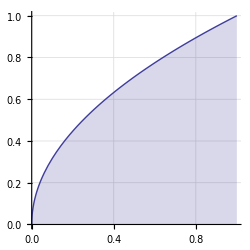

```mathematica
Plot[Sqrt[x], {x, 0, 1}, GridLines->Automatic, GridLinesStyle->LightGray,
Filling -> Axis , AspectRatio->1] (* Note: Axes equal *)
```

```mathematica
Integrate[Sqrt[n], {n, 0, 1}]
```

2/3

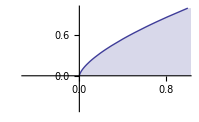

```mathematica
Plot[x^(2/3), {x, -10, 10}, 
GridLines->None, PlotRange->{{-0.5,1}, {-0.5, 1}},
Filling -> Axis]
```

```mathematica
(* Definite sum *)
{∑_(n=1)^5 5^n, 5^1+5^2+5^3+5^4+5^5}
```

{3905,3905}

```mathematica
(* Definite product *)
{∏_(n=1)^3 5^n, 5^1*5^2*5^3}
```

{15625,15625}

```mathematica
(* Definite product *)
{∏_(n=1)^3 5n, (5*1)*(5*2)*(5*3)}
```

{750,750}

```mathematica
GCD[6,15] (* Greatest common divisor *)
```

3

```mathematica
a:=({{2, 4}, {6, 5}}); a[[2,2]]
```

5

```mathematica
Sum[a,10]
```

{{∑_10 2,∑_10 4},{∑_10 6,∑_10 5}}

```mathematica
a = 10;
{(a^2-25), (a-5)(a+5)}
```

{75,75}

```mathematica
{(a-20)^2, (a^2+40a-400)}
```

{100,100}

```mathematica
{(a-20)^3, (a-20)(a^2+40a-400)}
```

{-1000,-1000}

```mathematica
(* The complete idiot's guide to Algebra *)(* Additive inverse property: The number that gives the additive identity element (0) as result. *)
2+(-2)
(* Multiplicative inverse property. The number that gives the multiplicative identity element (1) as result *)
{5*1/5, -6-1/6}
```

0

{1,1}

```mathematica
(1/2-2/7)/(1/7) (* = (7/14-4/14)/1/7 = 3/14/1/7 = 3/14*7/1 = 21/14 = 3/2 *)
```

3/2

```mathematica
(*  Careful with these! No.1: The opposite of 3 squared, which is -9.  No.2: (-3)(-3)=9  *)
{-3^2, (-3)^2}
```

{-9,9}

```mathematica
(* RULE, what to solve before the other: "Please Excuse My Dear Aunt Sally" *)
(* Solve this way: 1) (P)arantheses 2) (E)xponents/Powers 3) (M)ultiplication/(D)ivision 4) (A)ddition/(S)ubtraction *)
(* When two rules are in the same operation, like multiplication/division, solve from left to right. That is: 10^2/5^2*3 = (100/25)*3 = 4*3 = 12  *)
```

```mathematica
10^2÷5^2·3
```

4·3

```mathematica
{-4/5*-100/5, 400/25}
```

{16,16}

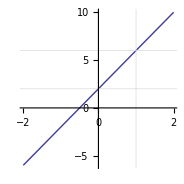

```mathematica
(* Chapter 5, solve for -4x+y=2: y=4x+2 *)
f[x_]:=4x+2
Plot[f[x], {x, -2, 2},GridLines->{{1}, {2,6}},
GridLinesStyle->LightGray,AspectRatio->1]
```

```mathematica
f[x_]:=-1/2 Abs[x+4]-3
```

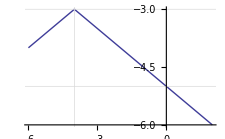

```mathematica
Plot[f[x], {x,-6, 2},GridLines->{{-4},{-3,-5}},
GridLinesStyle->LightGray]
```

```mathematica
f[x_]:=Abs[2x-4]+1
```

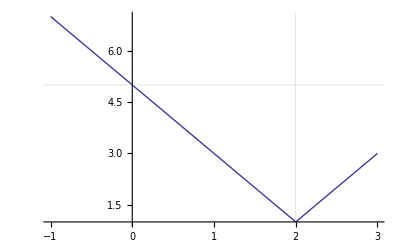

```mathematica
Plot[f[x], {x,-1, 3},GridLines->{{2},{5}},
GridLinesStyle->LightGray]
```

```mathematica
(* Chapter 6. Problem 1: Write the equation of the line with slope 4 that passes through the point (2(x1),–7(y1)) and solve the equation for y. (m=slope) *)
(* Usage: y-y1=m(x-x1). y-(-7)=4(x-2). y+7=4(x-2). y=4(x-2)-7. y=4x-8-7. Answer: y=4x-15 *)
```

```mathematica
f[x_]:=4x-15
```

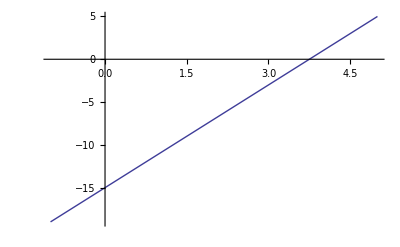

```mathematica
Plot[f[x], {x,-1, 5},GridLines->{{15/4}, {-15}}, (* NOTE: 15/4 to get x-axis intercept for y=0 *)
GridLinesStyle->LightGray]
```

```mathematica
(* Chapter 6. Problem 3: Graph the equation –2x–y=1 using the slope-intercept form. *)
(* –2x–y=1. -y=2x+1. (Multiply all by -1.) Result: y=-2x-1.
Put in x=0. y=2(0)-1. y=-1. Slope-intercept=(0,-1). Slope is 2 or -2/1 or 2/-1.
Note that coefficient/slope (2) is also a rational number (2/1)  *)
```

```mathematica
f[x_]:=-2x-1
```

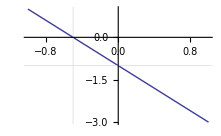

```mathematica
Plot[f[x], {x,-1, 1},GridLines->{{-0.5},{-1}},
GridLinesStyle->LightGray]
```

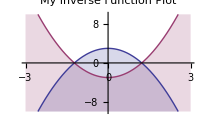

```mathematica
(* Example of inverse function (f2 "undoing" f1. Remember "Please Excuse My Dear Aunt Sally" rule! *)
f1[x_]:=-2 x^2+3;
f2[x_]:=x^2/(1/2)-3 (* NOTE: Inverse of -x^2 is x^2. *)
Plot[{f1[x], f2[x]}, {x,-3, 3},Filling->Bottom,
PlotLabel->"My Inverse Function Plot",
PlotRange->{Automatic, {-10, 10}}] (* NOTE: Two functions in one plot here *)
```

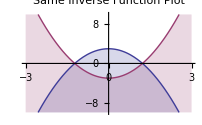

```mathematica
Plot[{-2 x^2+3, 2 x^2-3}, {x, -3, 3}, Filling -> Bottom,
PlotRange->{Automatic, {-10, 10}}, PlotLabel->"Same Inverse Function Plot"]
```

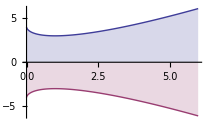

```mathematica
Plot[{2x-3 x^(2/3)+4, -2x+3 x^(2/3)-4}, {x, -6, 6}, Filling -> Axis,
PlotRange->Automatic,
GridLinesStyle->LightGray, GridLines-> None]
```

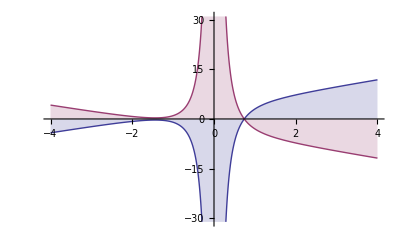

```mathematica
Plot[{2x-3 x^-2+4, -2x+3 x^-2-4}, {x, -4, 4}, Filling -> Axis,
PlotRange->Automatic,
GridLinesStyle->LightGray, GridLines-> None]
```

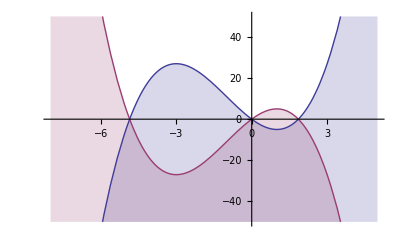

```mathematica
Plot[{x^3+3 x^2-9x, -x^3-3 x^2+9x}, {x, -8, 5}, PlotRange->{Automatic,{-50,50}},
Filling -> Bottom,GridLines-> None]
```

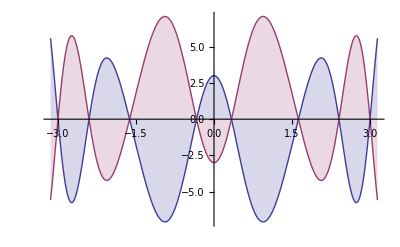

```mathematica
Plot[{3(Cos[4x]-2Sin[x^2]), (-3Cos[4x]+6Sin[x^2])}, {x, -Pi, Pi}, PlotRange->Automatic,
GridLines-> None, Filling -> Axis]
```

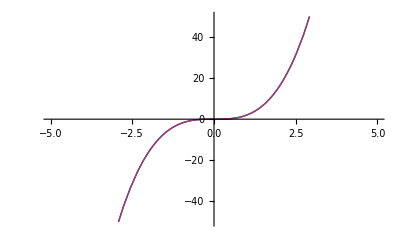

```mathematica
Plot[{2 x^3, 2/x^-3}, {x, -5, 5}, PlotRange->{Automatic,{-50,50}},
Filling -> None,GridLines-> None] (* NOTE: These two expressions are equal *)
```

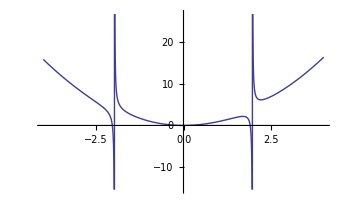

```mathematica
Plot[x^2+(x^3/(x^4-15)), {x, -4, 4}, 
GridLines->None,PlotRange->Automatic,
Filling -> None]
```

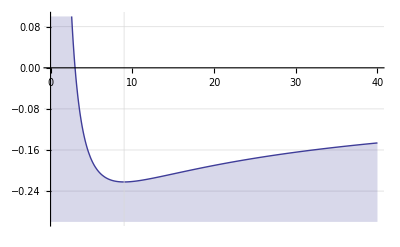

```mathematica
Plot[(2x+x-x^2)/x^(5/2), {x, -2, 40}, 
GridLines->{{9},Automatic},
PlotRange->{{0,40},{-0.3, 0.1}},
GridLinesStyle->{Cyan, LightGray},
Filling -> Bottom]
(* f[x_]:=(2x+x-x^2)/x^(5/2)  Solve[f'[x]==0,x]  Answer: {{x->9}} *)
```

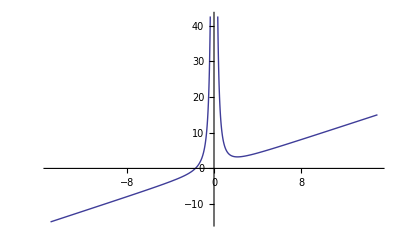

```mathematica
Plot[(x^3+5)/x^2, {x, -15, 15}, 
GridLines->None,PlotRange->Automatic,
Filling -> None]
```

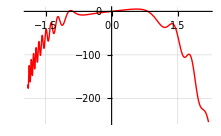

```mathematica
Plot[(Cos[x^5-3 x^4]-x^3)12x, {x, -1.9, 2.2}, 
GridLines->Automatic, GridLinesStyle->LightGray,
Filling -> None, PlotStyle->Red]
```

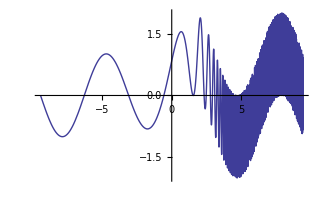

```mathematica
Plot[Sin[x] + Sin[Exp[x]],{x,-Pi*3,Pi*3}]
```

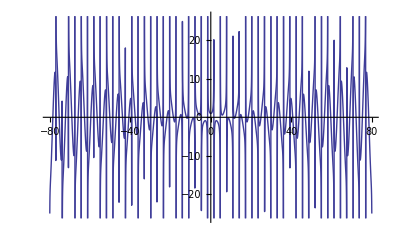

```mathematica
Plot[1/Cos[x]+Sin[x ]/5x,{x,-80,80}]
```

```mathematica
(* Some reciprocals to memorize... *)
{N[1/2^3], N[2^-3]}
```

{0.125,0.125}

```mathematica
{N[1/(3/2)], N[2/3]}
```

{0.666667,0.666667}

```mathematica
{N[1/2^(1/2)], N[2^(-1/2)]}
```

{0.707107,0.707107}

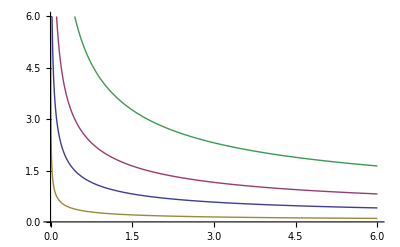

```mathematica
Plot[{1/x^(1/2), 2 x^(-1/2),1/(4 x^(1/2)),4 x^(-1/2)}, {x, 0, 6}, PlotRange->{Automatic,{0,6}},
Filling -> None,GridLines-> None]
```

```mathematica
(* IMPORTANT: Use dot (.) for matrix and vector multiplication in Mathematica. *)
(* The Complete Idiot's Guide To Algebra, Chapter 9, problem 4 below *)
({{2, -5}, {-3, 1}, {-4, 0}}).({{6, -2}, {-1, 3}})
```

{{17,-19},{-19,9},{-24,8}}

```mathematica
({{-8, 2}, {6, -3}}).({{2, 1, 5}, {-7, 3, 2}})
```

{{-30,-2,-36},{33,-3,24}}

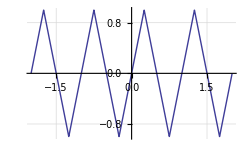

```mathematica
Plot[TriangleWave[x],{x,-2,2}, GridLines->Automatic,
GridLinesStyle->LightGray]
```

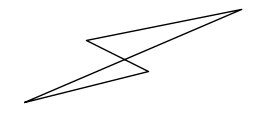

```mathematica
myPoints={{1,1},{5,2},{3,3},{8,4},{1,1}};
(* Plot the last variable *)
Graphics[Line[%]]
```

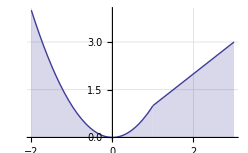

```mathematica
(* Plot a piecewise function *)
Plot[Piecewise[{{x^2,x<1},{x,x>1}}],{x,-2,3},
GridLines->Automatic, GridLinesStyle->LightGray,
Filling -> Bottom]
```

```mathematica
starColorPlot[star_]:=
Graphics3D[
{ColorData["BlackBodySpectrum"][AstronomicalData[star,"EffectiveTemperature"]],
Sphere[{0,0,3},Scaled[.15]]},Boxed->False,Lighting->{{"Ambient",Gray},
{"Directional",White,ImageScaled[{0,0,1}]}},PlotLabel->star];
starColorPlot/@{"Sun","Rigel","Sirius","Betelgeuse","Aldebaran","Capella",
"Vega","Arcturus","Castor","Pollux","Antares","Kochab","Altair","Regulus"}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}